# Gaussian Quadrature:

Firstly, See page 58 of the pdf attached to the email containing the 385 textbook


The following code is good to check your gaussian quadrature weights are working in one dimension, it is a built in mathematica function, dont change the 2. We are doing two point quadrature. In one dimension:   Starting at a and ending at b. (-1,1)

This function takes the number of points, and the length of the interval and it returns the points at which to evaluate the function, and a weight to multiply the function by. Generally an integral can be approximated by gaussian quadrature as:

∫_a^b f[x]ⅆx   is approximated as  ∑_(i=1)^n w_xf[x_i]

where n is the number of points, always 2 for us... Adding more must buy you more accuracy, you also need more if you have a higher degree polynomial idk why. The weights are just based on the interval.

In one dimension we need two points  x_i and one weight since in each dimension it seems like you use the same weight for both points  w_x

In two dimensions we need four points, X1 X2 Y1 Y2 and 2 weights Wx Wy

```mathematica
a = -1;
b = 1;
```

```mathematica
<<NumericalDifferentialEquationAnalysis`
list = GaussianQuadratureWeights[2, a,b]
```

{{-0.57735,1.},{0.57735,1.}}

For one point quadrature,the right hand side of (4.3.1) reduces to the midpoint method. For two point
quadrature the points are at a + β(b–a)  where β = 0.5 + 0.5/√3 or 0.5 – 0.5/√3

a and b are the starting and ending points of the interval. (b-a) is the length of the interval so expanded the point coordinates in each dimension are:

xpoint one: (start of x interval + half the length of the x interval) - half the length of the x interval/sqrt(3)
xpoint two: (start of x interval + half the length of the x interval) + half the length of the x interval/sqrt(3)

ypoint one: (start of y interval + half the length of the y interval) - half the length of the y interval/sqrt(3)
ypoint two: (start of y interval + half the length of the y interval) + half the length of the y interval/sqrt(3)

evaluate the function at each of these four points and multiply by (wx*wy), for each different element, wx (weight x) and wy (weight y) are the same

Here is a sample 2x2 element:

```mathematica
(* x and y coordinates *)
a = -1;
b = 1;
c = -1;
d = 1;
```

```mathematica
(* weights as described in loustaus email *)
wx = .5 * (b-a)
wy = .5*(d-c)
```

1.

1.

```mathematica
(* A sample function, in the actual thing remember that the function is a dot product of two gradients: gradPj dot gradPi *)

f[x_,y_] := x + y;
```

```mathematica
(* At this point I leave it to you to get the four points X1 X2 Y1 Y2 

and put them each into a list of the form:
 
pointsx = {x1,x2};
pointsy = {x1,x2};

*)
```

```mathematica
(*   If this is done correctly, the following two codeblocks should evaluate to the same value with little to no error, make sure to change  the initial a b c d values, re run everything in between, and then check that they still evaluate  the same. *)
```

```mathematica
∑_(i=1)^2 ∑_(j=1)^2 f[pointsx[[i]],pointsy[[j]]]*wx*wy
```

-4.44089×10^-16

```mathematica
∫_c^d ∫_a^b f[x,y]ⅆxⅆy
```

0

```mathematica
element
```

{1,1,11,12,2}

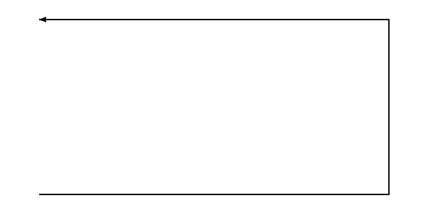

```mathematica
Show[Graphics[Arrow[nodes[[element[[2;;5]],2;;3]]]]]
```

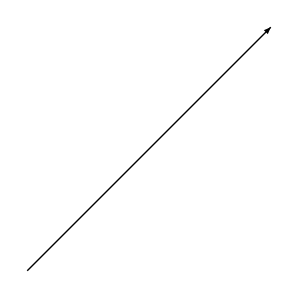

```mathematica
Show[Graphics[Arrow[{{0,0},{1,1}}]]]
```

```mathematica
knByn = ConstantArray[0,{188,188}];

For[i = 1, i ≤ 155, ++i, 

Print[i];
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[2]];
δ = nodes[[element[[2;;5]]]][[3]][[3]];
(*Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];*)

polynomials = {n1[α,β,γ,δ,x,y],n2[α,β,γ,δ,x,y],n3[α,β,γ,δ,x,y],n4[α,β,γ,δ,x,y]};

pointsx = {α + (γ-α)*(.5 - .5/Sqrt[3]),α + (γ-α)*(.5 + .5/Sqrt[3])};
pointsy = {β+ (δ-β)*(.5 - .5/Sqrt[3]),β+ (δ-β)*(.5 + .5/Sqrt[3])};


wx =.5*( γ - α);
wy =.5*(δ-β );

For[j = 1,j ≤ 4, j++, 

nj = element[[2;;5]][[j]];

js =  {D[polynomials[[j]],x],
D[polynomials[[j]],y]};

For[k =1, k ≤ 4, k ++, 

nk = element[[2;;5]][[k]];

ks = {D[polynomials[[k]],x],
D[polynomials[[k]],y]};

product =js.ks;
(* To be replaced with Gaussian Quadrature... 

knByn[[nj,nk]] += *)
Print[∫_β^δ ∫_α^γ productⅆxⅆy]
Print[∑_(ys=1)^2 ∑_(xs=1)^2 wx*wy*(product /.x-> pointsx[[xs]]/.y->pointsy[[ys]])];
];
];
];
```